# Mathematica Basics:

### We can define expressions and save them under a given name. No underscores! We will use ‘CamelCase’ instead. Note the semicolon suppresses output from any command (try removing it and running the cell with shift+enter)

```mathematica
myDifficultEquation=α^3+2 α^2-π α-√8;
```

### How did I type that? There are a lot of different ways to enter maths in mathematica. One is just with the keyboard:

```mathematica
x^2+Sqrt[3]
```

√3+x^2

### Another is with keyboard shortcuts. Most shortcuts start and end with the escape key. Try typing ESC+b+ESC in this cell.

```mathematica
β+x^2+Sqrt[3]
```

√3+x^2+β

### You can also use LATEX or html commands. Try typing ESC+\beta+ESC in this cell, or ESC+&beta;+ESC.

```mathematica
β+x^2+Sqrt[3]
```

√3+x^2+β

### There are shortcuts for powers, square roots and many other functions. But the most powerful way is with what mathematica calls a Palette. Look for Palettes in the menu and open the Basic Math Assistant. On the Basic Commands and Typesetting tabs of this Palette, you can find almost all of the mathematical symbols, functions and forms you would ever need. Try to open it and see if you can input the same expression as above: myDifficultEquation = α^3+2 α^2-π α-√8

```mathematica
myDifficultEquation
```

-2 √2-π α+2 α^2+α^3

### You can find a full list of input methods at https://reference.wolfram.com/language/tutorial/InputAndOutputInNotebooks.html Now let’s see what we can do with mathematica. First, let’s plot this expression. Note that every built-in name in Mathematica starts with upper case. To understand the options in 'Plot' try accessing the help system: Click on 'Plot' and press F1. Alternatively hover the mouse over the function and click '?' (On a Mac, Click on ‘Plot’ and press SHIFT+CMD+F).

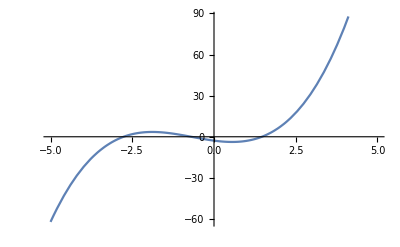

```mathematica
Plot[myDifficultEquation,{α,-5,5}]
```

### Let’s find solutions to this equation using ‘Solve’. Using N[...] we force a numerical evaluation (e.g. try N[Pi])

```mathematica
sols=Solve[myDifficultEquation==0]
N[sols]
```

{{α→Root-2.77Root[-2 √2-π #1+2 #1^2+#1^3&,1]-2.7660844908600972},{α→Root-0.698Root[-2 √2-π #1+2 #1^2+#1^3&,2]-0.6982808267908851},{α→Root1.46Root[-2 √2-π #1+2 #1^2+#1^3&,3]1.464365317650982}}

{{α→-2.76608},{α→-0.698281},{α→1.46437}}

### To substitute the solution back into an expression we use /. We also use Simplify to force simplification. Sometimes we must use FullSimplify, but that takes longer to evaluate. Note that % means “whatever was previously returned”.

```mathematica
x/.x->5
x*y/.x->Sin[3]/.y->ⅇ
```

5

ⅇ Sin[3]

```mathematica
myDifficultEquation/.sols
Simplify[%]
```

{-2 √2-π Root-2.77Root[-2 √2-π #1+2 #1^2+#1^3&,1]-2.7660844908600972+2 (Root-2.77Root[-2 √2-π #1+2 #1^2+#1^3&,1]-2.7660844908600972)^2+(Root-2.77Root[-2 √2-π #1+2 #1^2+#1^3&,1]-2.7660844908600972)^3,-2 √2-π Root-0.698Root[-2 √2-π #1+2 #1^2+#1^3&,2]-0.6982808267908851+2 (Root-0.698Root[-2 √2-π #1+2 #1^2+#1^3&,2]-0.6982808267908851)^2+(Root-0.698Root[-2 √2-π #1+2 #1^2+#1^3&,2]-0.6982808267908851)^3,-2 √2-π Root1.46Root[-2 √2-π #1+2 #1^2+#1^3&,3]1.464365317650982+2 (Root1.46Root[-2 √2-π #1+2 #1^2+#1^3&,3]1.464365317650982)^2+(Root1.46Root[-2 √2-π #1+2 #1^2+#1^3&,3]1.464365317650982)^3}

{0,0,0}

### We can evaluate Taylor expansions. To make the series a normal expression we must use Normal.

```mathematica
myImportantPhysics=Sin[x];
```

```mathematica
Series[myImportantPhysics,{x,0,8}]
Normal[%]
```

x-x^3/6+x^5/120-x^7/5040+O[x]^9

x-x^3/6+x^5/120-x^7/5040

### An alternative is to use //, which applies a function to what came before

```mathematica
Series[y/.y->Sin[x],{x,0,3}]//Normal
```

x-x^3/6

### We can evaluate derivatives in Mathematica

```mathematica
D[Sin[x], x]
```

Cos[x]

```mathematica
D[Sin[x], {x,2}]
```

-Sin[x]

```mathematica
D[Sin[x],{x,n}]
```

Sin[(n π)/2+x]

### A complicated example. Taylor expanding a badly behaved function. Play with the order of expansion!

(2 Cos[1/x])/x^3-Sin[1/x]/x^4

0.239134+2.34731 (-1.+x)-11.4839 (-1.+x)^2+30.7639 (-1.+x)^3

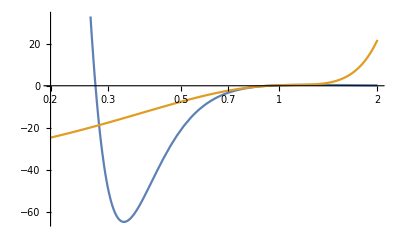

```mathematica
fullExpr=D[Sin[1/x],{x,2}]
%//FullSimplify;
Series[%,{x,1,3}];
simplExpr=%//N//Normal
LogLinearPlot[{fullExpr,simplExpr},{x,0.2,2}]
```

### We can find minima and maxima of functions

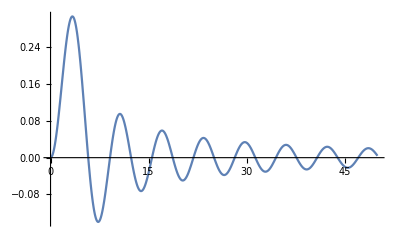

```mathematica
besselPlot=Plot[SphericalBesselJ[2, x],{x,0,50},PlotRange->Full]
```

```mathematica
point=FindMaximum[SphericalBesselJ[2, x],{x,30}]
```

{0.0336964,{x→29.7103}}

### We can create tables to represent vectors, or simply store many bits of information. We index with [[n]], which starts at 1 ! Also note here the syntax to write a For loop

```mathematica
table1 = {1.0, 2.0, 3.0}
table2 = Table[n^2,{n,0,5}]
Print[table1[[3]]]
For[n=1,n<Length[table2],n+=1, Print[table2[[n]]]]
```

{1.,2.,3.}

{0,1,4,9,16,25}

3.

0

1

4

9

16